```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
nmax=17;
a[0]=σz;(* Observable *)
For[i=1,i≤nmax,i++,
file = OpenRead["mt-dxa\\out-"<>ToString[i]<>".dxa"]; res = Read[file]; Close[file];
a[i]=(res/.{ii->I,S->1,koef->1}/.{cx->σx,cy->σy,cz->σz})I^i/i!//Expand
]
```

```mathematica
a[6]/.{v->1,σx->3/5,σy->0,σz->4/5}
```

-778160192/1953125

```mathematica
AbsoluteTiming[Do[
aa[n]=a[n]/.{v->1.,σx->3./5,σy->0.,σz->4./5},
{n,0,nmax}
]]
```

{0.0599975,Null}

```mathematica
aa[10]
```

-4374.65

```mathematica
Sum[aa[n] t^n,{n,0,nmax}]
```

0.8-6.5664 t^2+69.8358 t^4-398.418 t^6+1514.88 t^8-4374.65 t^10+10694.7 t^12-24539.4 t^14+57413.3 t^16

```mathematica
myPlot[vv_,px_,py_,pz_]:=Module[{
},
Do[
aa[n]=a[n]/.{v->vv,σx->px,σy->py,σz->pz},
{n,0,nmax}
];
Plot[{Sum[aa[n] t^n,{n,0,nmax}],Sum[aa[n] t^n,{n,nmax-1,nmax}]},{t,0,3},PlotRange->{-1.05,1.05}]
]
```

```mathematica
Sum[aa[n] t^n,{n,nmax-1,nmax}]
```

t^16 ((68719476736 v)/44341171875+(2342568067072 v^2)/28423828125+(698307661791232 v^3)/2519384765625+(1101719881865592832 v^4)/692830810546875+(63797381389882753024 v^5)/17320770263671875+(8636203958400974848 v^6)/1154718017578125+(99344288920904700755968 v^7)/10825481414794921875+(1107783065413365746830336 v^8)/90212345123291015625+(90156908093540483525632 v^9)/10825481414794921875+(46643251856581219456 v^10)/5623626708984375+(52985287425751595008 v^11)/17320770263671875+(63278480093380352 v^12)/27713232421875+(1452048881549312 v^13)/2519384765625+(19592112627712 v^14)/73901953125+(320767787008 v^15)/8868234375+(214761472 v^16)/354729375)

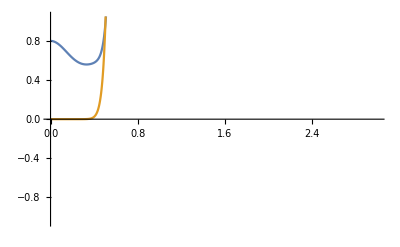

```mathematica
myPlot[1,3/5,0,4/5]
```

```mathematica
Manipulate[
Do[
aa[n]=a[n]/.{v->vv,σx->px,σy->py,σz->pz},
{n,0,nmax}
];
Show[
Plot[Sum[aa[n] t^n,{n,nmax-1,nmax}],{t,0,3},PlotRange->{-1.05,1.05}],
Plot[Sum[aa[n] t^n,{n,0,nmax}],{t,0,3},PlotRange->{-1.05,1.05}]
],
{{vv,1},0,2,0.1},
{{px,3/5},0,1,0.1},
{{py,0},0,1,0.1},
{{pz,4/5},0,1,0.1}
]
```